```mathematica
Quit[]
```

```mathematica
$LoadAddOns={"FeynArts","FeynHelpers"};
Needs["FeynCalc`"]
```

FeynCalc 9.3.1 (stable version). For help, use the documentation center, check out the wiki or visit the forum.

To save your and our time, please check our FAQ for answers to some common FeynCalc questions.

See also the supplied examples. If you use FeynCalc in your research, please cite

• V. Shtabovenko, R. Mertig and F. Orellana, Comput.Phys.Commun. 256 (2020) 107478, arXiv:2001.04407.

• V. Shtabovenko, R. Mertig and F. Orellana, Comput.Phys.Commun. 207 (2016) 432-444, arXiv:1601.01167.

• R. Mertig, M. Böhm, and A. Denner, Comput. Phys. Commun. 64 (1991) 345-359.

FeynArts 3.11 (25 Mar 2022) patched for use with FeynCalc, for documentation see the manual or visit www.feynarts.de.

If you use FeynArts in your research, please cite

• T. Hahn, Comput. Phys. Commun., 140, 418-431, 2001, arXiv:hep-ph/0012260

FeynHelpers 1.3.0, for more information see the accompanying publication.

Have a look at the supplied examples. If you use FeynHelpers in your research, please cite

• V. Shtabovenko, "FeynHelpers: Connecting FeynCalc to FIRE and Package-X", Comput. Phys. Commun., 218, 48-65, 2017, arXiv:1611.06793

Furthermore, remember to cite the authors of the tools that you are calling from FeynHelpers, which are

• FIRE by A. Smirnov, if you are using the function FIREBurn.

• Package-X by H. Patel, if you are using the function PaXEvaluate.

```mathematica
SetDirectory[NotebookDirectory[]];
```

```mathematica
CKM = IndexDelta;
Neglect[ME] = Neglect[ME2] = 0;
$FAVerbose=1;
(* use generic model from FeynCalc! The SUNF and SUNT functions in the .mod file have to be replaced by FASUNF and FASUNT *)
SetOptions[InsertFields, Model ->"../../Models/Top-EFTphysical_simple-FA/Top-EFTphysical_simple-FA",ExcludeParticles->{S[1]},InsertionLevel-> {Particles}];
SetOptions[Paint, PaintLevel -> {Particles}];
SetOptions[CreateTopologies, ExcludeTopologies -> {TadpoleCTs,Tadpoles, WFCorrectionCTs,SelfEnergies,SelfEnergyCTs}];
```

## u u → t t (EFT)

generic model {../../Models/Top-EFTphysical_simple-FA/Top-EFTphysical_simple-FA_FC} initialized

classes model {../../Models/Top-EFTphysical_simple-FA/Top-EFTphysical_simple-FA} initialized

in total: 2 Particles insertions

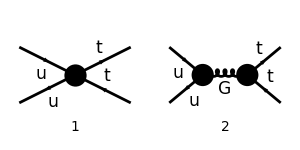

```mathematica
tops0 = CreateTopologies[0,2->2,  ExcludeTopologies -> {TadpoleCTs,Tadpoles,SelfEnergies}];
processGGT =  { F[7],-F[7]} -> {F[9],-F[9]};
allDiags = InsertFields[tops0,processGGT, InsertionLevel-> {Particles},ExcludeParticles->{V[1],S[1],S[2],S[3],V[2],V[3],F[7],F[6],F[5],F[8],F[9]},GenericModel->"../../Models/Top-EFTphysical_simple-FA/Top-EFTphysical_simple-FA_FC"];
goodDiags=allDiags;
Paint[goodDiags,ColumnsXRows->{2,1},ImageSize->{ 300,150},PaintLevel->{Particles},Numbering->Simple,AutoEdit->True,SheetHeader->None];
```

```mathematica
ampA=FCFAConvert[CreateFeynAmp[goodDiags,PreFactor->1,Truncated->False]/.{SUNT->FASUNT},IncomingMomenta->{k1,k2},OutgoingMomenta->{p1,p2},LoopMomenta->{q},List->False,DropSumOver->True,SMP->True,List->False,Contract->True,ChangeDimension->D,UndoChiralSplittings->True,FinalSubstitutions-> (M$FACouplings/.GS->gs)]/.{GS->gs,A0->Cg MT,B0->Cq/6};
ampB =FullSimplify[SUNSimplify[DiracSimplify[ampA]]]
```

in total: 2 Particles amplitudes

-1/6 ⅈ (1/(p1+p2)^2 6 gs T_Col2Col1^Glu5 T_Col3Col4^Glu5 (2 Cg MT (2 MT (φ(-k2)).γ^Lor2.(φ(k1)) ((φ(p1,MT)).γ^Lor2.(γ̄)^6.(φ(-p2,MT))+(φ(p1,MT)).γ^Lor2.(γ̄)^7.(φ(-p2,MT)))-((φ(p1,MT)).(γ̄)^6.(φ(-p2,MT))+(φ(p1,MT)).(γ̄)^7.(φ(-p2,MT))) ((φ(-k2)).(γ·p1).(φ(k1))-(φ(-k2)).(γ·p2).(φ(k1))))+gs (φ(-k2)).γ^Lor2.(φ(k1)) (φ(p1,MT)).γ^Lor2.(φ(-p2,MT)))+Cq (3 δ_Col1Col3 δ_Col2Col4-δ_Col1Col2 δ_Col3Col4) (φ(-k2)).γ^Ind25.(φ(k1)) (φ(p1,MT)).γ^Ind25.(γ̄)^6.(φ(-p2,MT)))

```mathematica
ampC =ampB/.{LorentzIndex[a_,D]->LorentzIndex[μ,D]}
```

-1/6 ⅈ (1/(p1+p2)^2 6 gs T_Col2Col1^Glu5 T_Col3Col4^Glu5 (2 Cg MT (2 MT (φ(-k2)).γ^μ.(φ(k1)) ((φ(p1,MT)).γ^μ.(γ̄)^6.(φ(-p2,MT))+(φ(p1,MT)).γ^μ.(γ̄)^7.(φ(-p2,MT)))-((φ(p1,MT)).(γ̄)^6.(φ(-p2,MT))+(φ(p1,MT)).(γ̄)^7.(φ(-p2,MT))) ((φ(-k2)).(γ·p1).(φ(k1))-(φ(-k2)).(γ·p2).(φ(k1))))+gs (φ(-k2)).γ^μ.(φ(k1)) (φ(p1,MT)).γ^μ.(φ(-p2,MT)))+Cq (3 δ_Col1Col3 δ_Col2Col4-δ_Col1Col2 δ_Col3Col4) (φ(-k2)).γ^μ.(φ(k1)) (φ(p1,MT)).γ^μ.(γ̄)^6.(φ(-p2,MT)))

```mathematica
(* Remove SM contribution *)
ampSM=gs^2 SeriesCoefficient[ampC,{gs,0,2},{yDM,0,0}];
ampC=Simplify[ampC-ampSM];
```

## On - Shell Case :

```mathematica
FCClearScalarProducts[];
SetMandelstam[s,t,u,k1,k2,-p1,-p2,0,0,MT,MT];
```

```mathematica
ampE = FullSimplify[Collect[Simplify[(  ampC)/.aS->GS^2/(4 Pi),Assumptions->{GS>0}],{Pair[LorentzIndex[μ,D],Momentum[p1,D]],Pair[LorentzIndex[μ,D],Momentum[p2,D]],DiracGamma[LorentzIndex[μ,D],D].DiracGamma[6],DiracGamma[LorentzIndex[μ,D],D].DiracGamma[7]},FullSimplify]];
```

```mathematica
(* Peskin A.38: ∑_A Subscript[T, ij]^A Subscript[T, kl]^A = 1/2 (Subscript[δ, i,l] Subscript[δ, j,k] - 1/3 Subscript[δ, i,j] Subscript[δ, k,l]) *)
(* 6 ∑_A Subscript[T, c2c1]^A Subscript[T, c3c4]^A =  3 Subscript[δ, c2,c4] Subscript[δ, c1,c3] - Subscript[δ, c1,c2] Subscript[δ, c3,c4] *)
ampEsimp=FullSimplify[ampE//.{(3*SUNFDelta[SUNFIndex[Col1],SUNFIndex[Col3]]*SUNFDelta[SUNFIndex[Col2],SUNFIndex[Col4]]-SUNFDelta[SUNFIndex[Col1],SUNFIndex[Col2]]*SUNFDelta[SUNFIndex[Col3],SUNFIndex[Col4]])-> -6SUNTF[{SUNIndex[Glu5]},SUNFIndex[Col2],SUNFIndex[Col1]]*SUNTF[{SUNIndex[Glu5]},SUNFIndex[Col3],SUNFIndex[Col4]]}]
```

ⅈ T_Col2Col1^Glu5 T_Col3Col4^Glu5 ((φ(-k2)).γ^μ.(φ(k1)) ((Cq-(4 Cg gs MT^2)/(p1+p2)^2) (φ(p1,MT)).γ^μ.(γ̄)^6.(φ(-p2,MT))-(4 Cg gs MT^2 (φ(p1,MT)).γ^μ.(γ̄)^7.(φ(-p2,MT)))/(p1+p2)^2)+(2 Cg gs MT ((φ(p1,MT)).(γ̄)^6.(φ(-p2,MT))+(φ(p1,MT)).(γ̄)^7.(φ(-p2,MT))) ((φ(-k2)).(γ·p1).(φ(k1))-(φ(-k2)).(γ·p2).(φ(k1))))/(p1+p2)^2)

```mathematica
ampEsimp2 = FeynAmpDenominatorExplicit[ampEsimp]
```

ⅈ T_Col2Col1^Glu5 T_Col3Col4^Glu5 ((φ(-k2)).γ^μ.(φ(k1)) ((Cq-(4 Cg gs MT^2)/s) (φ(p1,MT)).γ^μ.(γ̄)^6.(φ(-p2,MT))-(4 Cg gs MT^2 (φ(p1,MT)).γ^μ.(γ̄)^7.(φ(-p2,MT)))/s)+(2 Cg gs MT ((φ(p1,MT)).(γ̄)^6.(φ(-p2,MT))+(φ(p1,MT)).(γ̄)^7.(φ(-p2,MT))) ((φ(-k2)).(γ·p1).(φ(k1))-(φ(-k2)).(γ·p2).(φ(k1))))/s)

```mathematica
ampEsimp4=FullSimplify[DiracSimplify[DiracSimplify[ampEsimp2,DiracSubstitute5->True]/.(DiracGamma[7]->1-DiracGamma[6])]]
```

1/s ⅈ T_Col2Col1^Glu5 T_Col3Col4^Glu5 ((φ(-k2)).γ^μ.(φ(k1)) (Cq s (φ(p1,MT)).γ^μ.(γ̄)^6.(φ(-p2,MT))-4 Cg gs MT^2 (φ(p1,MT)).γ^μ.(φ(-p2,MT)))+2 Cg gs MT (φ(p1,MT)).(φ(-p2,MT)) ((φ(-k2)).(γ·p1).(φ(k1))-(φ(-k2)).(γ·p2).(φ(k1))))

```mathematica
sps=Cases2[ampEsimp4,Spinor]
moms=Cases2[ampEsimp4,DiracGamma]
```

{φ(k1),φ(-k2),φ(p1,MT),φ(-p2,MT)}

{(γ̄)^6,γ^μ,γ·p1,γ·p2}

```mathematica
ampF=Collect[ampEsimp4,{sps[[2]].moms[[2]].sps[[1]],sps[[3]].moms[[2]].DiracGamma[6].sps[[4]],sps[[3]].moms[[2]].sps[[4]],sps[[2]].moms[[3]].sps[[1]],sps[[2]].moms[[4]].sps[[1]]},FullSimplify]
```

(φ(-k2)).γ^μ.(φ(k1)) (ⅈ Cq T_Col2Col1^Glu5 T_Col3Col4^Glu5 (φ(p1,MT)).γ^μ.(γ̄)^6.(φ(-p2,MT))-(4 ⅈ Cg gs MT^2 T_Col2Col1^Glu5 T_Col3Col4^Glu5 (φ(p1,MT)).γ^μ.(φ(-p2,MT)))/s)+(2 ⅈ Cg gs MT T_Col2Col1^Glu5 T_Col3Col4^Glu5 (φ(p1,MT)).(φ(-p2,MT)) (φ(-k2)).(γ·p1).(φ(k1)))/s-(2 ⅈ Cg gs MT T_Col2Col1^Glu5 T_Col3Col4^Glu5 (φ(p1,MT)).(φ(-p2,MT)) (φ(-k2)).(γ·p2).(φ(k1)))/s

```mathematica
Collect[ampF,{Cq,Cg},FullSimplify]
```

ⅈ Cq T_Col2Col1^Glu5 T_Col3Col4^Glu5 (φ(-k2)).γ^μ.(φ(k1)) (φ(p1,MT)).γ^μ.(γ̄)^6.(φ(-p2,MT))-(2 ⅈ Cg gs MT T_Col2Col1^Glu5 T_Col3Col4^Glu5 (2 MT (φ(-k2)).γ^μ.(φ(k1)) (φ(p1,MT)).γ^μ.(φ(-p2,MT))+(φ(p1,MT)).(φ(-p2,MT)) ((φ(-k2)).(γ·p2).(φ(k1))-(φ(-k2)).(γ·p1).(φ(k1)))))/s

### Coefficients for each term

```mathematica
factor=FeynAmpDenominator[PropagatorDenominator[Momentum[p1+p2,D],0]]SUNTF[{SUNIndex[Glu5]},SUNFIndex[Col2],SUNFIndex[Col1]]*SUNTF[{SUNIndex[Glu5]},SUNFIndex[Col3],SUNFIndex[Col4]];
CVV = Coefficient[ ampF,factor sps[[2]].moms[[2]].sps[[1]] sps[[3]].moms[[2]].sps[[4]]]
CVR=Coefficient[ampF s FeynAmpDenominator[PropagatorDenominator[Momentum[p1+p2,D],0]],factor sps[[2]].moms[[2]].sps[[1]] sps[[3]].moms[[2]].DiracGamma[6].sps[[4]]]
CP1=Coefficient[ampF,factor sps[[2]].moms[[3]].sps[[1]] sps[[3]].sps[[4]]]
CP2=Coefficient[ampF,factor sps[[2]].moms[[4]].sps[[1]] sps[[3]].sps[[4]]]
Coeffs={CVV,CVR,CP1,CP2};
```

-4 ⅈ Cg gs MT^2

0

2 ⅈ Cg gs MT

-2 ⅈ Cg gs MT

## Coefficients for the EFT limit from the 1-loop calculation:

```mathematica
CVVeft=((ⅈ gs^2 MT^2 yDM^2 (2 mChi^6+3 mST^2 mChi^4+12 mST^2 log(mST/mChi) mChi^4-6 mST^4 mChi^2+mST^6))/(96 (mChi^2-mST^2)^4 π^2));
CVReft=-((ⅈ gs^2 s (12 log(mChi/mST) mChi^6-11 mChi^6+18 mST^2 mChi^4-9 mST^4 mChi^2+2 mST^6) yDM^2)/(576 (mChi^2-mST^2)^4 π^2));
CP1eft=-((ⅈ gs^2 MT yDM^2 (2 mChi^6+3 mST^2 mChi^4-12 mST^2 log(mChi/mST) mChi^4-6 mST^4 mChi^2+mST^6))/(192 (mChi^2-mST^2)^4 π^2));
CP2eft=-CP1eft;
```

```mathematica
A0B0sol=Solve[{CVV==CVVeft,CVR==CVReft},{Cg,Cq}]
```

{}

```mathematica
Solve[{CP1==CP1eft,CP2==CP2eft},A0]
```

{}

## Coefficients from Matchete/MatchMakerEFT:

```mathematica
A0match=(-gs*yDM^2*MT/(384*Pi^2))*(mST^6/mChi^6+2*(1-(3*mST^4)/mChi^4)+(3*mST^2*(1+4*Log[mST/mChi]))/mChi^2)/(mChi^2*(1-mST^2/mChi^2)^4);
B0match=(gs^2*yDM^2/(3456*Pi^2))*(6*mChi^6*Log[mChi^2/mST^2]-11*mChi^6+18*mST^2*mChi^4-9*mST^4*mChi^2+2*mST^6)/((mChi^2-mST^2)^4);
```

```mathematica
FullSimplify[A0match-A0/.A0B0sol,Assumptions->{mST>0,mChi>0}]
FullSimplify[B0match-B0/.A0B0sol,Assumptions->{mST>0,mChi>0}]
```

-A0-(gs MT yDM^2 (3 mChi^4 mST^2-6 mChi^2 mST^4+12 mChi^4 mST^2 log(mST/mChi)+2 mChi^6+mST^6))/(384 π^2 (mChi^2-mST^2)^4)

(gs^2 yDM^2 (18 mChi^4 mST^2-9 mChi^2 mST^4+12 mChi^6 log(mChi/mST)-11 mChi^6+2 mST^6))/(3456 π^2 (mChi^2-mST^2)^4)-B0